```mathematica
Nt = 455(*551*) ;(*151*)
ti = 0; tf =5(*1*); 
deltat = (tf - ti) /Nt ;
Nx = 455(*551*); (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = 0; xf = 40;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.125

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];

deltax = X[[2]] - X[[1]];
deltat = T[[2]] - T[[1]];

f[x_] = ⅇ^(- 8(x-π)^2);
(*f[x_] = ⅇ^(- (x)^2);
f[x_] = ⅇ^(- ((x-xi)*((2*Pi))/(xf-xi))^2);*)

fexact[t_,x_] = ⅇ^(- 8((x-t)-π)^2);
(*fexact[t_,x_] = ⅇ^(- ((((x-xi)*((2*Pi))/(xf-xi))-t))^2)*)
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
(*CN*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
UCN = Chop[UCN, 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]


I1 = N[IdentityMatrix[Length[D1]],32];
A = N[I1 - ((DL / 2)),32];
B = N[I1 + ((DL / 2)),32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = Developer`ToPackedArray[EMCN, Real]; 

Do[UCN[[n+1,All]] = UCN[[n,All]] + (EMCN ).UCN[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*RK2*)
URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[X],32];
URK2 = Chop[URK2, 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]

IRK2 = N[IdentityMatrix[Length[DL]],32];

MRK2 = N[(IRK2 + (DL) + ((1/2)*(MatrixPower[DL,2]))),32];

EMRK2 = N[MRK2 - IRK2,32];

EMRK2= Developer`ToPackedArray[EMRK2, Real]; 

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK4*)
URK4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK4[[1,All]] = N[f[X],32];
URK4 = Chop[URK4, 10^(-307)];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]

IRK4 = N[IdentityMatrix[Length[DL]],32];

MRK4 = N[IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4])),32];

EMRK4 = N[MRK4 - IRK4,32];

EMRK4= Developer`ToPackedArray[EMRK4, Real]; 

Do[URK4[[n+1,All]] = URK4[[n,All]] + (EMRK4).URK4[[n,All]], {n,1,Nt - 1 }]
```

True

$Aborted

```mathematica
(*LD4*)
UN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UN[[1,All]] = N[f[X],32];
UN = Chop[UN, 10^(-307)];
UN = Developer`ToPackedArray[UN, Real]; 
Developer`PackedArrayQ[UN]


IN = N[IdentityMatrix[Length[D1]],32];
AN = N[IN - ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
BN = N[IN + ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
MN = N[Inverse[AN].BN,32];
EMN = N[MN - IN,32];

EMN= Developer`ToPackedArray[EMN, Real]; 

Do[UN[[n+1,All]] = UN[[n,All]] + (EMN).UN[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD6*)
ULD6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD6[[1,All]] = N[f[X],32];
ULD6 = Chop[ULD6, 10^(-307)];
ULD6 = Developer`ToPackedArray[ULD6, Real]; 
Developer`PackedArrayQ[ULD6]


ILD6 = N[IdentityMatrix[Length[D1]],32];
ALD6 = N[ILD6 - ((DL / 2)) + (((MatrixPower[DL,2])/10)) - (((MatrixPower[DL,3])/120)),32];
BLD6 = N[ILD6 + ((DL / 2)) + (((MatrixPower[DL,2])/10)) + (((MatrixPower[DL,3])/120)),32];
MLD6 = N[Inverse[ALD6].BLD6,32];
EMLD6 = N[MLD6 - ILD6,32];

EMLD6= Developer`ToPackedArray[EMLD6, Real]; 

Do[ULD6[[n+1,All]] = ULD6[[n,All]] + (EMLD6).ULD6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK6*)
URK6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK6[[1,All]] = N[f[X],32];
URK6 = Chop[URK6, 10^(-307)];
URK6 = Developer`ToPackedArray[URK6, Real]; 
Developer`PackedArrayQ[URK6]

IRK6 = N[IdentityMatrix[Length[DL]],32];


MRK6 = N[IRK6 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4])) + ((1/120) * (MatrixPower[DL,5])) + ((1/720) * (MatrixPower[DL,6])),32];

EMRK6 = N[MRK6 - IRK6,32];

EMRK6= Developer`ToPackedArray[EMRK6, Real]; 

Do[URK6[[n+1,All]] = URK6[[n,All]] + (EMRK6).URK6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD8*)
ULD8= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD8[[1,All]] = N[f[X],32];
ULD8 = Chop[ULD8, 10^(-307)];
ULD8 = Developer`ToPackedArray[ULD8, Real]; 
Developer`PackedArrayQ[ULD8]


ILD8 = N[IdentityMatrix[Length[D1]],32];
ALD8 = N[ILD8 - ((DL / 2)) + (((3*MatrixPower[DL,2])/28)) - (((MatrixPower[DL,3])/84)) + (((MatrixPower[DL,4])/1680)),32];
BLD8 = N[ILD8 + ((DL / 2)) + (((3*MatrixPower[DL,2])/28)) + (((MatrixPower[DL,3])/84)) + (((MatrixPower[DL,4])/1680)),32];
MLD8 = N[Inverse[ALD8].BLD8,32];
EMLD8 = N[MLD8 - ILD8,32];

EMLD8= Developer`ToPackedArray[EMLD8, Real]; 

Do[ULD8[[n+1,All]] = ULD8[[n,All]] + (EMLD8).ULD8[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*Now we don't need D1 or DL to have 32 digit accuracy so can put it into a packed array*)
D1 = Developer`ToPackedArray[D1, Real];
DL = Developer`ToPackedArray[DL, Real];
```

```mathematica
(************************************************************************************************************************)
(*Eigenvalues*)
(************************************************************************************************************************)
```

```mathematica
(*CN*)
evals = Eigenvalues[N[MCN]];
realEvals = Re[evals];
imagEvals = Im[evals];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
(*ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*RK2*)
evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
(*ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*RK4*)
evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
(*ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*LD4*)
evalsN = Eigenvalues[N[MN]];
realEvalsN= Re[evalsN];
imagEvalsN = Im[evalsN];
(*ListPlot[{Transpose[{realEvalsN,imagEvalsN}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
FCN = Developer`ToPackedArray[FCN, Real];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
intCN = Developer`ToPackedArray[intCN, Real];
Do[
FCN[[i]] = (D1.UCN[[i,All]])^2;

intCN[[i]] = (2π)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];
```

```mathematica
(*RK2*)
FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
FRK2 = Developer`ToPackedArray[FRK2, Real];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = Developer`ToPackedArray[intRK2, Real];
Do[
FRK2[[i]] = (D1.URK2[[i,All]])^2;

intRK2[[i]] = (2π)/Nx Total[FRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*RK4*)
FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
FRK4 = Developer`ToPackedArray[FRK4, Real];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
intRK4 = Developer`ToPackedArray[intRK4, Real];
Do[
FRK4[[i]] = (D1.URK4[[i,All]])^2;

intRK4[[i]] = (2π)/Nx Total[FRK4[[i,All]]]
,{i,1,Length[FRK4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK4}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*LD4*)
FN = Table[0,{i,1,Nt},{j,1,Nx}];
FN = Developer`ToPackedArray[FN, Real];
intN = Table[0,{i,1,Length[FN[[All,1]]]}];
intN = Developer`ToPackedArray[intN, Real];
Do[
FN[[i]] = (D1.UN[[i,All]])^2;

intN[[i]] = (2π)/Nx Total[FN[[i,All]]]
,{i,1,Length[FN[[All,1]]]}];
(*ListPlot[{Transpose[{T,intN}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
energyErrorLD4 = Abs[intN - intN[[1]]];
energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];
energyErrorRK4 = Abs[intRK4 - intRK4[[1]]];
```

```mathematica
(*LD2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD2}], PlotRange->Full]*)
```

```mathematica
(*LD4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD4}], PlotRange->Full]*)
```

```mathematica
(*RK2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK2}], PlotRange->Full]*)
```

```mathematica
(*RK4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK4}], PlotRange->Full]*)
```

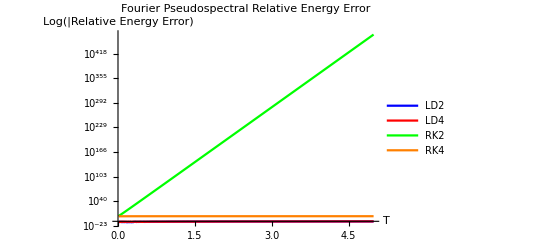

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}]},PlotStyle->{Blue, Red,Green, Orange},PlotLegends->{"LD2","LD4","RK2","RK4"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Fourier Pseudospectral Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorRK4]}},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
```

ⅇ^(-(-t+x)^2)

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)
```

```mathematica
(*RK2*)
abserrRK2 = Abs[URK2-Uexact];
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
errorRK2 = Developer`ToPackedArray[errorRK2, Real];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

```mathematica
(*LD4*)
abserrLD4 = Abs[UN-Uexact];
errorLD4 = Table[0,{i,1,Length[abserrLD4]}];
errorLD4 = Developer`ToPackedArray[errorLD4, Real];
Do[
errorLD4[[i]] = Norm[abserrLD4[[i,All]], 1] * deltax;
,{i,1,Length[errorLD4]}
];
(*ListLinePlot[Transpose[{T,errorLD4}]]*)
```

```mathematica
(*RK4*)
abserrRK4 = Abs[URK4-Uexact];
errorRK4 = Table[0,{i,1,Length[abserrRK4]}];
errorRK4 = Developer`ToPackedArray[errorRK4, Real];
Do[
errorRK4[[i]] = Norm[abserrRK4[[i,All]], 1] * deltax;
,{i,1,Length[errorRK4]}
];
(*ListLinePlot[Transpose[{T,errorRK4}],PlotRange->All]*)
```

```mathematica
(*RK6*)
abserrRK6 = Abs[URK6-Uexact];
errorRK6 = Table[0,{i,1,Length[abserrRK6]}];
errorRK6 = Developer`ToPackedArray[errorRK6, Real];
Do[
errorRK6[[i]] = Norm[abserrRK6[[i,All]], 1] * deltax;
,{i,1,Length[errorRK6]}
];
```

```mathematica
(*LD6*)
abserrLD6 = Abs[ULD6-Uexact];
errorLD6 = Table[0,{i,1,Length[abserrLD6]}];
errorLD6 = Developer`ToPackedArray[errorLD6, Real];
Do[
errorLD6[[i]] = Norm[abserrLD6[[i,All]], 1] * deltax;
,{i,1,Length[errorLD6]}
];
```

```mathematica
(*LD8*)
abserrLD8 = Abs[ULD8-Uexact];
errorLD8 = Table[0,{i,1,Length[abserrLD8]}];
errorLD8 = Developer`ToPackedArray[errorLD8, Real];
Do[
errorLD8[[i]] = Norm[abserrLD8[[i,All]], 1] * deltax;
,{i,1,Length[errorLD8]}
];
```

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorRK2}], Transpose[{T,errorLD4}], Transpose[{T,errorRK4}],Transpose[{T,errorLD6}],Transpose[{T,errorRK6}],Transpose[{T,errorLD8}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-4}}, PlotStyle->{Blue,Green,Red,Orange,Pink,Yellow, Gray},PlotLegends->{"LD2","RK2","LD4","RK4","RK6","LD6","LD8"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[{Transpose[{T,errorLD6}],Transpose[{T,errorRK6}],Transpose[{T,errorLD8}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-14}}, PlotStyle->{Blue,Green,Red},PlotLegends->{"RK6","LD6","LD8"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

-Graphics-

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4,errorLD6,errorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Error_PS.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,URK4[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{0,2*Pi},{0,1}}], {n,1,Nt ,1} ]
```

```mathematica
Animate[ListLinePlot[Transpose[{X,(UCN[[n]] - Uexact[[n]])}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]
```

```mathematica
(********************************************************************************************************************)
(*Start/Final*)
(********************************************************************************************************************)

(*LD2*)
LD2start = UCN[[1]];
LD2startErr = UCN[[1]] - Uexact[[1]];
LD2end = Last[UCN];
LD2endErr = Last[UCN] - Last[Uexact];

(*LD4*)
LD4start = UN[[1]];
LD4startErr = UN[[1]] - Uexact[[1]];
LD4end = Last[UN];
LD4endErr = Last[UN] - Last[Uexact];

(*RK2*)
RK2start = URK2[[1]];
RK2startErr = URK2[[1]] - Uexact[[1]];
RK2end = Last[URK2];
RK2endErr = Last[URK2] - Last[Uexact];

(*RK4*)
RK4start = URK4[[1]];
RK4startErr = URK4[[1]] - Uexact[[1]];
RK4end = Last[URK4];
RK4endErr = Last[URK4] - Last[Uexact];

(*exportData=Flatten/@Transpose[{X,LD2start, LD2startErr, LD2end, LD2endErr,RK2start, RK2startErr, RK2end, RK2endErr, LD4start, LD4startErr, LD4end, LD4endErr,RK4start, RK4startErr, RK4end, RK4endErr}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\start_final_PS.dat",exportData,"Table"];*)
```

```mathematica
(*Tutorial for way to eliminate roundoff error. paste inside a help window*)
(*tutorial/NDSolveSPRK#1464293172*)
```